```mathematica
(* Constants and Functions *)
h = 6.6*10^-34;
c = 3*10^8;
kb = 1.38*10^-23;
lrot=56*100;
lvr = 40*100;
Ts = 300;
Ttp=200;
B[ν_,T_]:=2*h*c^2*ν^3/(Exp[h*c*ν/(kb*T)]-1)
```

```mathematica
(* Calculate the Forcing for doubling RH *)
Frot = lrot*Log[75/37.5]*π*(B[800*100,300]-B[150*100,200])
Fvr = lvr*Log[75/37.5]*π*(B[1200*100,300]-B[1500*100,200])
F = Frot+Fvr
```

13.9969

5.69786

19.6948

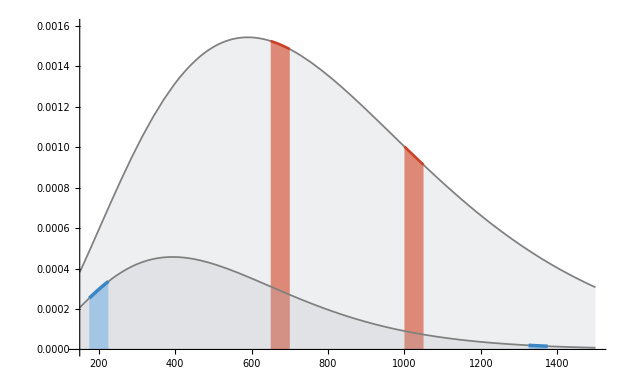

```mathematica
(* Make Graphics for Planck Function *)
p1 = Plot[B[100*ν,Ts],{ν,150,1500},PlotStyle->{Gray,Thickness[.002]},Filling->Bottom,FillingStyle->RGBColor[170/255,175/255,185/255,0.2],PlotRange->{{150,1500},{0,.0016}},Ticks->{Automatic,{}}];
p1left = Plot[B[100*ν,Ts],{ν,650,700},PlotStyle->{RGBColor[204/255,65/255,37/255,1],Thickness[.003]},Filling->Bottom,FillingStyle->RGBColor[221/255,126/255,107/255,0.9],PlotRange->{{150,1500},{0,.0016}},Ticks->{Automatic,{}}];
p1right = Plot[B[100*ν,Ts],{ν,1050,1000},PlotStyle->{RGBColor[204/255,65/255,37/255,1],Thickness[.003]},Filling->Bottom,FillingStyle->RGBColor[221/255,126/255,107/255,0.9],PlotRange->{{150,1500},{0,.0016}},Ticks->{Automatic,{}}];
p2 = Plot[B[100*ν,Ttp],{ν,150,1500},PlotStyle->{Gray,Thickness[.002]},Filling->Bottom,FillingStyle->RGBColor[170/255,175/255,185/255,0.2],PlotRange->{{150,1500},{0,.0016}},Ticks->{Automatic,{}}];
p2left = Plot[B[100*ν,Ttp],{ν,175,225},PlotStyle->{RGBColor[61/255,134/255,198/255,1],Thickness[.004]},Filling->Bottom,FillingStyle->RGBColor[158/255,195/255,230/255,0.9],PlotRange->{{150,1500},{0,.0016}},Ticks->{Automatic,{}}];
p2right = Plot[B[100*ν,Ttp],{ν,1325,1375},PlotStyle->{RGBColor[61/255,134/255,198/255,1],Thickness[.004]},Filling->Bottom,FillingStyle->RGBColor[158/255,195/255,230/255,0.9],PlotRange->{{150,1500},{0,.0016}},Ticks->{Automatic,{}}];
Show[p1,p1left,p1right,p2,p2left,p2right]



(*Graphics[{Pink,Disk[]},PlotRange->{{-.5,.5},{0,1.5}},PlotRangeClipping->True,Frame->True]*)
```



```mathematica
Plot[Sin[x],{x,0,10},Ticks->{Automatic,{}}]
```